```mathematica
parseRow[r_]:=If[StringMatchQ[#, NumberString],#//ToExpression,#]&/@StringSplit[r, "\t"]
```

```mathematica
cols={"GLOBALEVENTID","SQLDATE","MonthYear","Year","FractionDate","Actor1Code","Actor1Name","Actor1CountryCode","Actor1KnownGroupCode","Actor1EthnicCode","Actor1Religion1Code","Actor1Religion2Code","Actor1Type1Code","Actor1Type2Code","Actor1Type3Code","Actor2Code","Actor2Name","Actor2CountryCode","Actor2KnownGroupCode","Actor2EthnicCode","Actor2Religion1Code","Actor2Religion2Code","Actor2Type1Code","Actor2Type2Code","Actor2Type3Code","IsRootEvent","EventCode","EventBaseCode","EventRootCode","QuadClass","GoldsteinScale","NumMentions","NumSources","NumArticles","AvgTone","Actor1Geo_Type","Actor1Geo_FullName","Actor1Geo_CountryCode","Actor1Geo_ADM1Code","Actor1Geo_Lat","Actor1Geo_Long","Actor1Geo_FeatureID","Actor2Geo_Type","Actor2Geo_FullName","Actor2Geo_CountryCode","Actor2Geo_ADM1Code","Actor2Geo_Lat","Actor2Geo_Long","Actor2Geo_FeatureID","ActionGeo_Type","ActionGeo_FullName","ActionGeo_CountryCode","ActionGeo_ADM1Code","ActionGeo_Lat","ActionGeo_Long","ActionGeo_FeatureID","DATEADDED", "URL"};
```

```mathematica
Length@cols
```

58

```mathematica
csv=parseRow/@First/@Import["~/Desktop/TEMPORARY-GDELT/20150301.export.CSV"];
```

```mathematica
csv[[1]]//Dimensions
```

{44}

```mathematica
Position[cols, "Actor2Name"]
```

{{17}}

```mathematica
actors1=DeleteCases[Union[csv[[All,7]]],""];
nActors1[actor_]:=Length@DeleteDuplicates@Cases[csv,(x_/;x[[7]]==actor):>x[[17]]]
```

```mathematica
LaunchKernels[8]
nActorsByActor1=ParallelMap[nActors1,actors1];
CloseKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

{KernelObject[1,local,<defunct>],KernelObject[2,local,<defunct>],KernelObject[3,local,<defunct>],KernelObject[4,local,<defunct>],KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>],KernelObject[7,local,<defunct>],KernelObject[8,local,<defunct>]}

```mathematica
actors2=DeleteCases[Union[csv[[All,17]]],""];
nActors2[actor_]:=Length@DeleteDuplicates@Cases[csv,(x_/;x[[17]]==actor):>x[[7]]]
```

```mathematica
LaunchKernels[8]
nActorsByActor2=ParallelMap[nActors2,actors2];
CloseKernels[]
```

{KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

{KernelObject[9,local,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,local,<defunct>],KernelObject[12,local,<defunct>],KernelObject[13,local,<defunct>],KernelObject[14,local,<defunct>],KernelObject[15,local,<defunct>],KernelObject[16,local,<defunct>]}

```mathematica
n5Sum[x_]:={Text/@{"Min", "Q1", "Med", "Q3", "Max"}, {Min@x}~Join~Quartiles[x]~Join~{Max@x}}
```

```mathematica
Grid[
{Text/@{"# A2 by A1", "# A1 by A2"},{Grid[n5Sum[nActorsByActor1]],Grid[n5Sum[nActorsByActor2]]}},Frame->All]
```

# A2 by A1 | # A1 by A2
Min | Q1 | Med | Q3 | Max
1 | 1 | 3 | 9 | 670 | Min | Q1 | Med | Q3 | Max
1 | 1 | 3 | 9 | 651

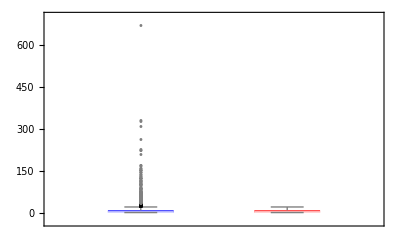

```mathematica
BoxWhiskerChart[{nActorsByActor1, nActorsByActor2},"Outliers",ChartStyle->{Blue,Red},ChartLegends->{"# Actors 2 per Actor 1", "# Actors 1 per Actor 2"}]
```

```mathematica
getTopK[x_,k_]:=First@First@Position[x, RankedMax[x,k]]
actors1[[getTopK[nActorsByActor1,#]&/@Range[5]]]
actors2[[getTopK[nActorsByActor2,#]&/@Range[5]]]
```

{UNITED STATES,POLICE,GOVERNMENT,PRESIDENT,UNITED KINGDOM}

{UNITED STATES,GOVERNMENT,PRESIDENT,POLICE,SCHOOL}

```mathematica
actors1[[First@First@Position[nActorsByActor1,Max[nActorsByActor1]]]]
```

UNITED STATES

```mathematica
actors2[[First@First@Position[nActorsByActor2,Max[nActorsByActor2]]]]
```

UNITED STATES

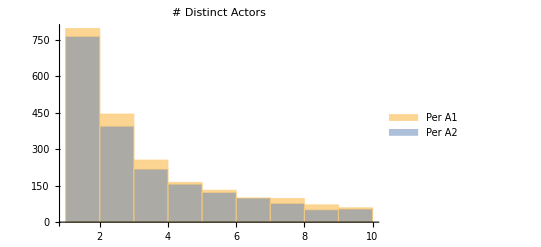

```mathematica
infreqBit1=nActorsByActor1<10//Thread;
infreqBit2=nActorsByActor2<10//Thread;
Histogram[{Pick[nActorsByActor1,infreqBit1],Pick[nActorsByActor2,infreqBit2] }, ChartLegends->{"Per A1", "Per A2"}, PlotLabel->"# Distinct Actors"]
```

```mathematica
infreqA1s=Pick[actors1,infreqBit1];
infreqA2s=Pick[actors2,infreqBit2];
Length@Intersection[infreqA1s,infreqA2s]/Length@Union[infreqA1s,infreqA2s]//N
```

0.609785

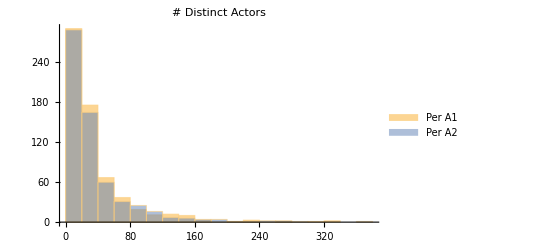

```mathematica
freqBit1=10≤nActorsByActor1<400// Thread;
freqBit2=10≤nActorsByActor2<400//Thread;
Histogram[{Pick[nActorsByActor1,freqBit1],Pick[nActorsByActor2,freqBit2] }, ChartLegends->{"Per A1", "Per A2"}, PlotLabel->"# Distinct Actors"]
```

```mathematica
BoxWhiskerChart[{nActorsByActor1, nActorsByActor2},"Outliers",ChartStyle->50,ChartLegends->{"# Actors 2 per Actor 1", "# Actors 1 per Actor 2"}]
```

```mathematica
Position[cols,"EventBaseCode"]
```

{{28}}

```mathematica
nEvents1[actor_]:=Length@DeleteDuplicates@Cases[csv,(x_/;x[[7]]==actor):>x[[28]]]
nEvents2[actor_]:=Length@DeleteDuplicates@Cases[csv,(x_/;x[[17]]==actor):>x[[28]]]
```

```mathematica
LaunchKernels[8];
nEventsByA1=ParallelMap[nEvents1,actors1];
nEventsByA2=ParallelMap[nEvents2,actors2];
CloseKernels[];
```

{KernelObject[17,local],KernelObject[18,local],KernelObject[19,local],KernelObject[20,local],KernelObject[21,local],KernelObject[22,local],KernelObject[23,local],KernelObject[24,local]}

{KernelObject[17,local,<defunct>],KernelObject[18,local,<defunct>],KernelObject[19,local,<defunct>],KernelObject[20,local,<defunct>],KernelObject[21,local,<defunct>],KernelObject[22,local,<defunct>],KernelObject[23,local,<defunct>],KernelObject[24,local,<defunct>]}

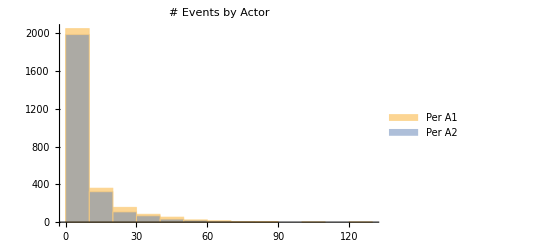

```mathematica
Histogram[{nEventsByA1, nEventsByA2},ChartLegends->{"Per A1", "Per A2"}, PlotLabel->"# Events by Actor"]
```

```mathematica
(* TODO: feed in geographic location of the city *)
(* TODO: categorize *)
```